```mathematica
Options[drawRadiation]={centralEngineSize->1,v->0.9,lowAngle->0.7,highAngle->0.07,observerDistance->100,observerAngle->0.6,photonSize->0.3,photonInterval->20};
drawRadiation[t_,OptionsPattern[]]:=Block[{i,ti},
Graphics[{
Disk[{0,0},OptionValue[centralEngineSize]],
{Red,Circle[{0,0},OptionValue[v]t,{-OptionValue[lowAngle],OptionValue[lowAngle]}]},
{Thick,Blue,Circle[{0,0},OptionValue[v]t,{-OptionValue[highAngle],OptionValue[highAngle]}]},
{Darker[Green],Arrow[{{0,0},{OptionValue[observerDistance]Cos[OptionValue[observerAngle]],OptionValue[observerDistance]Sin[OptionValue[observerAngle]]}}]},
Table[
Block[{startX,startY,angle,x,y},
startX=OptionValue[v]i Cos[Min[OptionValue[lowAngle],OptionValue[observerAngle]]];
startY=OptionValue[v]i Sin[Min[OptionValue[lowAngle],OptionValue[observerAngle]]];
angle=OptionValue[observerAngle];
x=startX+(t-i)Cos[angle];
y=startY+(t-i)Sin[angle];
{Red,Disk[{x,y},OptionValue[photonSize]]}
]
,{i,0,t,OptionValue[photonInterval]}],
Table[
Block[{startX,startY,angle,x,y},
startX=OptionValue[v]i Cos[Min[OptionValue[highAngle],OptionValue[observerAngle]]];
startY=OptionValue[v]i Sin[Min[OptionValue[highAngle],OptionValue[observerAngle]]];
angle=OptionValue[observerAngle];
x=startX+(t-i)Cos[angle];
y=startY+(t-i)Sin[angle];
{Blue,Disk[{x,y},OptionValue[photonSize]]}
]
,{i,0,t,OptionValue[photonInterval]}]
}]
];
```

```mathematica
Dynamic[Manipulate[drawRadiation[t],
{t,0,100}
]]
```

```mathematica
Options[drawScheme]={centralEngineSize->0.03,jetRadius->0.3,lowAngle->0.1,highAngle->0.01,observerSize->0.03,observerDistance->1,observerAngle->0.09,centralEngineQ->True,centralEngineLabelQ->False,jetQ->True,jetLabelQ->False,epQ->True,γQ->True,observerQ->True,observerLabelQ->False};
drawScheme[OptionsPattern[]]:=Block[{i,ti,redX,redY,blueX,blueY,observerX,observerY},
Graphics[{
{If[OptionValue[centralEngineQ],Opacity[1],Opacity[0]],Disk[{0,0},OptionValue[centralEngineSize]]},
{Black,If[OptionValue[centralEngineLabelQ],Opacity[1],Opacity[0]],Text["Central\nEngine",{0,-OptionValue[centralEngineSize]},Top]},

observerX=OptionValue[observerDistance]Cos[OptionValue[observerAngle]];
observerY=OptionValue[observerDistance]Sin[OptionValue[observerAngle]];
{Darker[Green],If[OptionValue[observerQ],Opacity[1],Opacity[0]],Disk[{observerX,observerY},OptionValue[observerSize]]},
{Darker[Green],If[OptionValue[observerLabelQ],Opacity[1],Opacity[0]],
Text["Observer",{observerX,observerY+OptionValue[centralEngineSize]},Bottom]},

{If[OptionValue[jetQ],Opacity[0.1],Opacity[0]],Red,Disk[{0,0},OptionValue[jetRadius],{-OptionValue[lowAngle],OptionValue[lowAngle]}]},
{Thick,Red,If[OptionValue[jetQ],Opacity[1],Opacity[0]],Circle[{0,0},OptionValue[jetRadius],{-OptionValue[lowAngle],OptionValue[lowAngle]}]},
{If[OptionValue[jetQ],Opacity[0.1],Opacity[0]],Blue,Disk[{0,0},OptionValue[jetRadius],{-OptionValue[highAngle],OptionValue[highAngle]}]},
{Thick,Blue,If[OptionValue[jetQ],Opacity[1],Opacity[0]],Circle[{0,0},OptionValue[jetRadius],{-OptionValue[highAngle],OptionValue[highAngle]}]},
{Red,If[OptionValue[jetLabelQ],Opacity[1],Opacity[0]],Text["Shock\nFront",{1.03OptionValue[jetRadius]Cos[OptionValue[lowAngle]/2],-OptionValue[jetRadius]Sin[OptionValue[lowAngle]/2]},{Left,Top}]},

redX=OptionValue[jetRadius] Cos[Min[OptionValue[lowAngle],OptionValue[observerAngle]]];
redY=OptionValue[jetRadius] Sin[Min[OptionValue[lowAngle],OptionValue[observerAngle]]];
blueX=OptionValue[jetRadius] Cos[Min[OptionValue[highAngle],OptionValue[observerAngle]]];
blueY=OptionValue[jetRadius] Sin[Min[OptionValue[highAngle],OptionValue[observerAngle]]];
{Red,If[OptionValue[epQ],Opacity[1],Opacity[0]],Line[{{0,0},{redX,redY}}]},
{Red,If[OptionValue[epQ],Opacity[1],Opacity[0]],Text[Style["e^±, p^±",FontSize->14],{redX/2,redY/2},{Right,Bottom}]},
{Blue,If[OptionValue[epQ],Opacity[1],Opacity[0]],Line[{{0,0},{blueX,blueY}}]},
{Blue,If[OptionValue[epQ],Opacity[1],Opacity[0]],Text["e^±, p^±",{blueX/2,blueY/2},{Left,Top}]},

{Dashed,If[OptionValue[γQ],Opacity[1],Opacity[0]],Red,Line[{{redX,redY},{observerX,observerY}}]},
{Red,If[OptionValue[γQ],Opacity[1],Opacity[0]],Text["γ",{(redX+observerX)/2,(redY+observerY)/2},{Right,Bottom}]},
{Dashed,If[OptionValue[γQ],Opacity[1],Opacity[0]],Blue,Line[{{blueX,blueY},{observerX,observerY}}]},
{Blue,If[OptionValue[γQ],Opacity[1],Opacity[0]],Text["γ",{(blueX+observerX)/2,(blueY+observerY)/2},{Left,Top}]}
}]
];
```

```mathematica
Dynamic[Manipulate[drawScheme[centralEngineSize->ces,jetRadius->jr,lowAngle->la,highAngle->ha,observerSize->os,observerDistance->od,observerAngle->oa,centralEngineLabelQ->True,jetLabelQ->True,observerLabelQ->True],
{ces,0,1},
{jr,0,1},
{la,0,π},
{ha,0,π},
{os,0,1},
{od,0,1},
{oa,0,π}
]]
```

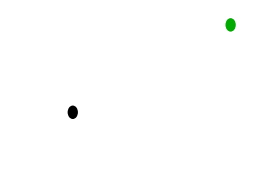
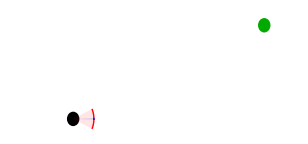
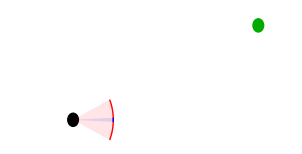
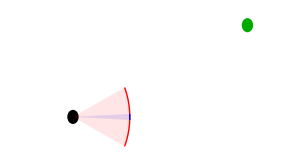
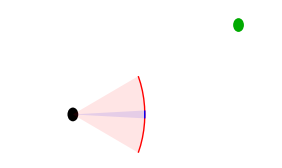
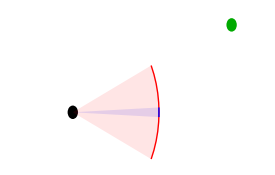
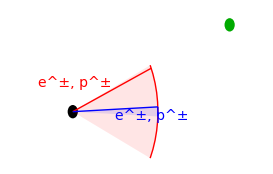
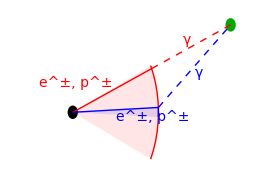
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Flatten[{
drawScheme[centralEngineSize->0.03,jetRadius->0.5,lowAngle->0.43,highAngle->0.043,observerSize->0.03,observerDistance->1,observerAngle->0.4,centralEngineQ->False,jetQ->False,epQ->False,γQ->False,observerQ->True,jetLabelQ->False],
drawScheme[centralEngineSize->0.03,jetRadius->0.5,lowAngle->0.43,highAngle->0.043,observerSize->0.03,observerDistance->1,observerAngle->0.4,centralEngineQ->True,jetQ->False,epQ->False,γQ->False,observerQ->True,jetLabelQ->False],
Table[drawScheme[centralEngineSize->0.03,jetRadius->jri,lowAngle->0.43,highAngle->0.043,observerSize->0.03,observerDistance->1,observerAngle->0.4,centralEngineQ->True,jetQ->True,epQ->False,γQ->False,observerQ->True,jetLabelQ->False],{jri,0,0.5,0.1}],
drawScheme[centralEngineSize->0.03,jetRadius->0.5,lowAngle->0.43,highAngle->0.043,observerSize->0.03,observerDistance->1,observerAngle->0.4,centralEngineQ->True,jetQ->True,epQ->True,γQ->False,observerQ->True,jetLabelQ->False],
drawScheme[centralEngineSize->0.03,jetRadius->0.5,lowAngle->0.43,highAngle->0.043,observerSize->0.03,observerDistance->1,observerAngle->0.4,centralEngineQ->True,jetQ->True,epQ->True,γQ->True,observerQ->True,jetLabelQ->False]
}]
```

```mathematica
0.03,0.5,0.43,0.043,0.03,1,0.4
```